```mathematica
f:N->N
```

f:N→N

```mathematica
n∈∧OddQ@f[n]∧EvenQ@f[f[n]]∧OddQ@f[f[f[n]]]
```

False

```mathematica
n∈∧OddQ@f[n]
```

False

```mathematica
EvenQ@f[n]
```

False

```mathematica
n==2k∧EvenQ[n]∧k∈
```

False

```mathematica
OddQ@f[n]
```

False

```mathematica
n==2k∧n∈∧EvenQ[n]∧k∈
```

False

```mathematica
FindEquationalProof[
ForAll[x,Exists[n,x==mult[two,n]]],{

}]
```

FindEquationalProof::invs: Invalid specification of propositions ∀_x∃_n x==mult[two,n] and axioms {}.

FindEquationalProof[∀_x∃_n x==mult[two,n],{}]

```mathematica
f:A->B
```

f:A→B

```mathematica
g:B->A
```

g:B→A

```mathematica
Composition[g,f]
```

g@*f

```mathematica
f:A->B∧g:B->A∧(g@*f):A->B∧(g@*f)^(n∈):A->B
```

```mathematica
(g@*f):A->B
```

```mathematica
even[n_]:=n/2
```

```mathematica
odd[n_]:=3n+1
```

```mathematica
even[n]
```

n/2

```mathematica
Apply[sum,Range@10]
```

sum[1,2,3,4,5,6,7,8,9,10]

```mathematica
Apply[Sum,Range@10]
```

∑_2 ∑_3 ∑_4 ∑_5 ∑_6 ∑_7 ∑_8 ∑_9 ∑_10 1

```mathematica
Apply[Times,Range@10]
```

3628800

```mathematica
AddTo[4]
```

AddTo::argr: AddTo called with 1 argument; 2 arguments are expected.

AddTo[4]

```mathematica
AddTo[4,1]
```

AddTo::rvalue: 4 is not a variable with a value, so its value cannot be changed.

4+=1

```mathematica
ConstantArray[{even,odd},1]
```

{{even,odd}}

```mathematica
ConstantArray[{even,odd},2]
```

{{even,odd},{even,odd}}

```mathematica
Apply[List,Range@10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
(3n+1)/2
```

1/2 (1+3 n)

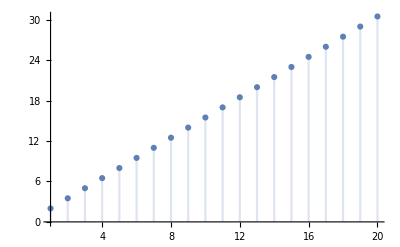

```mathematica
DiscretePlot[1/2 (1+3 n),{n,1,20}]
```

```mathematica
(3n+1)/2==2k+1
```

1/2 (1+3 n)==1+2 k

```mathematica
Reduce[1/2 (1+3 n)==1+2 k]
```

k==-1/4+(3 n)/4

```mathematica
k==(3 n)/4-1/4
```

k==-1/4+(3 n)/4

```mathematica
(3n+1)/2==2k
```

1/2 (1+3 n)==2 k

```mathematica
Reduce[1/2 (1+3 n)==2 k]
```

k==1/4+(3 n)/4